# Lie Theory, Featuring 3D Rotations

Brian Beckman

Mar 2026

In this notebook, we formalize the mathematical framework of Lie theory, using 3D rotations as a driving example. While we have previously applied Lie theory to rotational dynamics, we took many mathematical facts on faith. Here, in a structured, cheat-sheet style, we derive everything, proceeding from the central concept, the 𝔰𝔲(2) Lie algebra, to the SO(3) and SU(2) rotational Lie groups, which emerge naturally via representation theory.

In short, this notebook serves as a physics-centric introduction to Lie theory, showing techniques that generalize far beyond 3D rotations.

## Preliminaries

```mathematica
ClearAll[proof];
proof[v_]/;BooleanQ[v]:=(If[v,
Print[Style["QED■",StandardGreen,Bold,18]],
Print[Style["FAILED PROOF■",StandardRed,Bold,18]]];v);
proof[___]:=Print[Style["INVALID INPUT TO PROOF■",StandardYellow,Bold,18]];
```

## Lie Ontology

One of the most important applications of Lie theory is for 3D rotations. In two earlier notebooks, SO(3) for Classical Mechanics and SU(2) for Classical Mechanics, we showed how to solve dynamical problems via geodesics in the Lie groups SO(3) and SU(2), with metric tensors composed of kinetic energies. We demonstrated the superiority of SU(2) in avoiding the gimbal lock in the Euler-angle parameterization of SO(3), by honoring the intrinsic, simply connected topology of the configuration space of rotations. In those notebooks, we developed just enough of the mathematical theory to assure the application, in a “just-in-time” style. This style left us with several pieces of theory “on the table.” Here, we organize those pieces and fit them together in a tidy structure that’s easy to understand, to remember, and to be creative with. We first give an inventory of the objects and mappings in the theory, and then present a diagram linking them together. In the rest of the notebook, we work out the details formally, machine-checked by Wolfram.

### Object Inventory

The “big picture” for rotations is that we can 	represent the abstract Lie algebra 𝔤 of 𝔰𝔲(2) in at least two ways. One of them leads us to SO(3) and its troubles with gimbal lock (via the non-trivial fundamental group π_1(SO(3))=ℤ_2), the other to SU(2) with no such troubles and, thus, a virtuous slippery slope to quantum theory.

Representation is a formal notion: mapping the abstraction to matrices. Representation theory itself is an immense topic. Here we need just a basic understanding.

Abstractly, a Lie algebra is a vector space with a Lie bracket operation, [A,B], that satisfies the Jacobi identity, [A,[B,C]]+[C,[A,B]]+[B,[C,A]]=0. In a matrix representation, the Lie bracket is the matrix commutator [A,B]=A·B-B·A.

The abstract algebra, 𝔤, for 3D rotations is characterized by its its specific structure constants. In general, the structure constants f_ijk  of any Lie algebra-qua-vector-space are the Lie bracket applied to a choice of basis vectors: [E_i,E_j]=f_ijk E_k (sum over k). The specific structure constants for rotations are ϵ_ijk, the fully antisymmetric Levi-Civita tensor, where i, j, k are in {1,2,3}. These structure constants model the cross product, familiar from elementary physics as the primary tool for describing rotation.  In the real domain, these structure constants imply the generators J_k. In the complex domain, they imply the generators T_k. The corresponding Lie groups follow via the exponential map.

A Lie group is both a group and a differentiable manifold. As a manifold, it enjoys parameterization by coordinate charts that must be differentiable where they overlap. As a group, its elements describe linear transformations of other objects, spinors and mat-vecs in our running example.

The adjoint action, Q·v·Q† is linear in v.

The double-covering of SO(3) by SU(2) follows from the topology of their respective manifolds. SO(3) is diffeomorphic to the real projective space ℝP^3, visualized as the 3-sphere S^3, where every point is identified with its antipode, (q∼(-q)). ℝP^3 is not simply connected because any closed loop in S^3 that includes both q and -q, the same point in ℝP^3, is a closed loop in ℝP^3 that cannot be shrunk to zero size without “tearing”. In contrast, SU(2) is diffeomorphic to S^3. This space is simply connected because any closed path can be shrunk to zero size.

S^3 is the set of all points q≡(q_0,q_1,q_2,q_3) in ℝ^4 such that (q_0^2+q_1^2+q_2^2+q_3^2=1).

In ℝP^3, points are actually pairs (q,-q) of elements of ℝ^4.

The elements of each group describe linear transformations of geometric objects that are not elements of the group. Concretely, we represent the linear transformations as n×n matrices that operate on n-vectors. We represent SO(3) by real 3×3 rotation matrices that act on real 3-vectors. We represent SU(2) by complex 2×2 matrices, isomorphic to unit quaternions, that act on spinors in V_spin=ℂ^2 and on complex, 2×2, traceless, Hermitian matrices (mat-vecs in 𝔥_σ) that represent real 3-vectors.

The algebra 𝔰𝔲(2) is isomorphic to the pure imaginary quaternions, (0,q_1,q_2,q_3).

Finally, we introduce some notation, ad_X and Ad_Q, for actions in the Lie algebra and the Lie Group respectively, and the Killing form for extracting components of members of the Lie groups.

```mathematica
Module[{data,header,row},
row[col1_,col2_,col3_]:={col1,col2,col3};
header={Style["Short Name",14,Bold],
Style["Item Description",14,Bold],
Style["Context / Physical Interpretation",14,Bold]};
data={header,
row["𝔤","Abstraction of 𝔰𝔲(2)","Abstract Lie algebra: [E_i, E_j] = ε_ijk E_k (no sum)"],
row["f_ijk","Structure Constants","Numbers ε_ijk characterizing the bracket"],
row["σ_k","Pauli Matrices","Basis {σ_1, σ_2, σ_3} for the Pauli Map"],
row["T_k","Generators of 𝔰𝔲(2)_(ℂ^2)","T_k = -ⅈ σ_k/2; [T_i,T_j] = T_k in ℂ^2×ℂ^2"],
row["J_k","Generators of 𝔰𝔲(2)_(ℝ^3)","[J_i,J_j] = J_k in ℝ^3×ℝ^3"],
row["𝔰𝔲(2)_(ℂ^2)","𝔰𝔲(2) 2x2 ℂ Rep","Complex matrix representation (Generators T_k)"],
row["𝔰𝔲(2)_(ℝ^3) = 𝔰𝔬(3)","𝔰𝔬(3) 3x3 ℝ Rep","Real matrix representation (Generators J_k)"],
row["SU(2)","SU(2) Group","2 × 2 unitary matrices, det=1"],
row["SO(3)","SO(3) Group","3 × 3 orthogonal matrices, det=1"],
row["V_spin","Spinors (ℂ^2)","Space for Fundamental Action of SU(2)"],
row["ℝ^3","Real ℝ^3","Euclidean space of physical 3-vectors"],
row["𝔥_σ","Mat-Vecs","Traceless Hermitian 2 × 2 matrices"],
row["𝒵","Center","The kernel {I, -I} of the SU(2) → SO(3) map"],
row["S^3","Topology S^3","Topology of SU(2) (3-sphere)"],
row["ℝ^3P","Topolog ℝ^3P","Topology of SO(3) (Projective space)"],
row["ad_XY","Infitesimal adjoint","Algebra action [X,Y]"],
row["Ad_QZ","Finite Adjoint","Group action Q·Z·Q†"],
row["B","Killing Form","Trace inner product for coordinate extraction"]};
Grid[data,
Alignment->{Left,Baseline},(*Spacings->{2,1.25},*)
Dividers->{None,{
1->Directive[White,Thickness[2]],
2->White,
7->Directive[White,Thickness[0.5],Opacity[0.3]],
12->Directive[White,Thickness[0.5],Opacity[0.3]],
17->Directive[White,Thickness[0.5],Opacity[0.3]],
-1->White}},
Background->{None,{GrayLevel[0.2],{GrayLevel[0.15],GrayLevel[0.12]}}},
ItemStyle->{White,12,FontFamily->"Times"},
ItemSize->{{8,12,25},Automatic}]]
```

Short Name | Item Description | Context / Physical Interpretation
𝔤 | Abstraction of 𝔰𝔲(2) | Abstract Lie algebra: [E_i, E_j] = ε_ijk E_k (no sum)
f_ijk | Structure Constants | Numbers ε_ijk characterizing the bracket
σ_k | Pauli Matrices | Basis {σ_1, σ_2, σ_3} for the Pauli Map
T_k | Generators of 𝔰𝔲(2)_(ℂ^2) | T_k = -ⅈ σ_k/2; [T_i,T_j] = T_k in ℂ^2×ℂ^2
J_k | Generators of 𝔰𝔲(2)_(ℝ^3) | [J_i,J_j] = J_k in ℝ^3×ℝ^3
𝔰𝔲(2)_(ℂ^2) | 𝔰𝔲(2) 2x2 ℂ Rep | Complex matrix representation (Generators T_k)
𝔰𝔲(2)_(ℝ^3) = 𝔰𝔬(3) | 𝔰𝔬(3) 3x3 ℝ Rep | Real matrix representation (Generators J_k)
SU(2) | SU(2) Group | 2 × 2 unitary matrices, det=1
SO(3) | SO(3) Group | 3 × 3 orthogonal matrices, det=1
V_spin | Spinors (ℂ^2) | Space for Fundamental Action of SU(2)
ℝ^3 | Real ℝ^3 | Euclidean space of physical 3-vectors
𝔥_σ | Mat-Vecs | Traceless Hermitian 2 × 2 matrices
𝒵 | Center | The kernel {I, -I} of the SU(2) → SO(3) map
S^3 | Topology S^3 | Topology of SU(2) (3-sphere)
ℝ^3P | Topolog ℝ^3P | Topology of SO(3) (Projective space)
ad_XY | Infitesimal adjoint | Algebra action [X,Y]
Ad_QZ | Finite Adjoint | Group action Q·Z·Q†
B | Killing Form | Trace inner product for coordinate extraction

### Mapping Inventory

Here we list, non-exhaustively, various mappings amongst the objects above. MatrixExp takes us from a representation of an element of a Lie algebra to a representation of an element of a Lie Group. This is a surjection in that multiple inputs can produce the same output. Not listed is the inverse, MatrixLog, which goes the other way, because it is multi-valued, but there is an example in the body of the notebook of how to choose a branch of that inverse.

Technically, MatrixExp is always a surjection exactly when the target Lie group is compact and connected. SO(3) and SU(2) satisfies these criteria. See Hall, Knapp, and Milnor in the References.

The center 𝒵 of a group is the set of all elements that commute with every other element of the group . For SU(2), the center consists of only I, the identity, and -I, the negative identity. The inclusion map f merely states that f(I)=I and f(-I)=-I. This inclusion formally ensures that SU(2)/𝒵 is isomorphic to SO(3) in that both I and -I in SU(2) map to I in SO(3), expressing the “double cover” relationship between SU(2) and SO(3). In group-theoretic terms, 𝒵 is the kernel of the SU(2)->SO(3) map, the set of elements in the domain that map to the identity element.

The Pauli map takes 3-vectors to traceless, Hermitian matrices (mat-vecs) in 𝔥_σ. The trace projection takes them back, via a circuitous derivation involving the Killing Form, B. Examples are shown in the body of the notebook.

To concretely represent the vectors in the Lie-algebra-qua-vector space, we must choose a basis. Many choices map to the same structure constants f_ijk, and that’s why the mapping is only surjective. However, once a basis is chosen for 𝔰𝔲(2) and the structure constants are materialized as the specific constants ϵ_ijk, the mapping becomes bijective in that we can recover the basis from the particular structure constants ϵ_ijk.

The remaining rows of the Mapping Inventory should be self-explanatory given the previous explanations.

```mathematica
Module[{data,header,row},(*Helper to keep the data structure clean*)row[src_,target_,mech_,type_]:={src,target,mech,type};
header=Style[#,14,Bold]&/@{"Source","Target","Name / Mechanism","Type"};
data={header,
row["𝔰𝔲(2)","SU(2)","MatrixExp","Surj"],
row["𝔰𝔬(3)","SO(3)","MatrixExp","Surj"],
row["SU(2)","SO(3)","Adjoint Rep / 2-to-1 Cover","Surj (2:1)"],
row["𝒵","SU(2)","Center inclusion","Inj"],
row["ℝ^3","𝔥_σ","Pauli Map (v · σ)","Bij"],
row["𝔥_σ","ℝ^3","Trace Projection (getTCoeffs)","Bij"],
row["𝔰𝔲(2)","𝔰𝔬(3)","Algebra Ad Rep (TtoJ)","Bij"],
row["𝔤","f_ijk","Basis Mapping","Surj"],
row["SU(2)","S^3","Topo ID","Bij (Diffeo)"],
row["SO(3)","ℝ^3P","Topo ID","Bij (Diffeo)"],
row["SU(2)×V_spin","V_spin","Fundamental Action (Q ψ)","Act"],
row["SU(2)×𝔥_σ","𝔥_σ","Adjoint Action (Q Z Q†)","Act"],
row["SO(3)×ℝ^3","ℝ^3","Standard Rot (R v)","Act"]};
Grid[data,
Alignment->{Left,Baseline},
(*Spacings->{2,1.5},*)
Dividers->{None,{
1->Directive[White,Thickness[2]],
2->White,
7->Directive[White,Thickness[0.5],Opacity[0.3]],
12->Directive[White,Thickness[0.5],Opacity[0.3]],
-1->White}},
Background->{None,{GrayLevel[0.2],{GrayLevel[0.15],GrayLevel[0.12]}}},
ItemStyle->{White,12,FontFamily->"Times"},
ItemSize->{{7,5,15,7},Automatic}]]
```

Source | Target | Name / Mechanism | Type
𝔰𝔲(2) | SU(2) | MatrixExp | Surj
𝔰𝔬(3) | SO(3) | MatrixExp | Surj
SU(2) | SO(3) | Adjoint Rep / 2-to-1 Cover | Surj (2:1)
𝒵 | SU(2) | Center inclusion | Inj
ℝ^3 | 𝔥_σ | Pauli Map (v · σ) | Bij
𝔥_σ | ℝ^3 | Trace Projection (getTCoeffs) | Bij
𝔰𝔲(2) | 𝔰𝔬(3) | Algebra Ad Rep (TtoJ) | Bij
𝔤 | f_ijk | Basis Mapping | Surj
SU(2) | S^3 | Topo ID | Bij (Diffeo)
SO(3) | ℝ^3P | Topo ID | Bij (Diffeo)
SU(2)×V_spin | V_spin | Fundamental Action (Q ψ) | Act
SU(2)×𝔥_σ | 𝔥_σ | Adjoint Action (Q Z Q†) | Act
SO(3)×ℝ^3 | ℝ^3 | Standard Rot (R v) | Act

### Ontology Diagram

This diagram clarifies the relationships between the objects and mappings. These relationships will be clarified in the proofs in the body of the notebook.

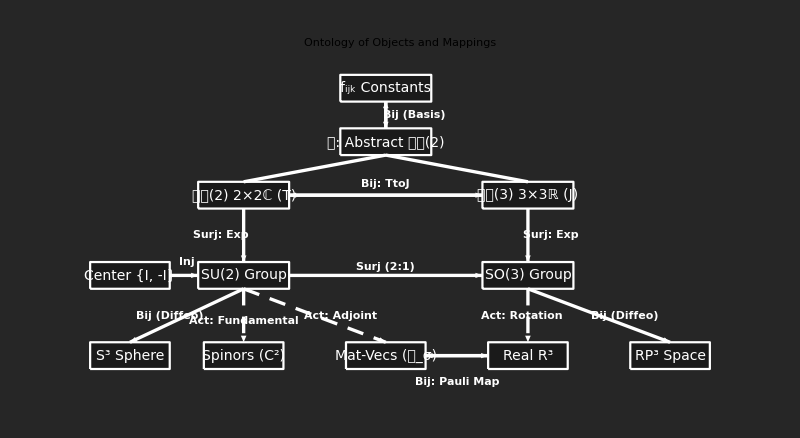

```mathematica
Module[{node, lbl},
 (* Helper functions for consistent styling *)
 node[pos_, txt_, color_: GrayLevel[0.1], w_: 0.8] := {
   EdgeForm[{White, Thickness[0.002]}], color, 
   Rectangle[pos - {w, 0.25}, pos + {w, 0.25}, RoundingRadius -> 0.1], 
   White, Text[Style[txt, 14], pos]
  };
 
 lbl[pos_, txt_] := {
   Text[Style[txt, 11, Bold, Background -> GrayLevel[0.15]], pos]
  };

 Graphics[{
   node[{0, 5}, "f_ijk Constants"], 
   node[{0, 4}, "𝔤: Abstract 𝔰𝔲(2)"], 
   node[{-2.5, 3}, "𝔰𝔲(2) 2×2ℂ (T)"], 
   node[{2.5, 3}, "𝔰𝔬(3) 3×3ℝ (J)"], 
   node[{-4.5, 1.5}, "Center {I, -I}", GrayLevel[0.1], 0.7], 
   node[{-2.5, 1.5}, "SU(2) Group"], 
   node[{2.5, 1.5}, "SO(3) Group"], 
   node[{-4.5, 0}, "S^3 Sphere", GrayLevel[0.1], 0.7], 
   node[{-2.5, 0}, "Spinors (C^2)", GrayLevel[0.1], 0.7], 
   node[{0, 0}, "Mat-Vecs (𝔥_σ)", GrayLevel[0.1], 0.7], 
   node[{2.5, 0}, "Real R^3", GrayLevel[0.1], 0.7], 
   node[{5.0, 0}, "RP^3 Space", GrayLevel[0.1], 0.7], 
   (* EDGES *)
   Thickness[0.003], Arrowheads[0.02], White, 
   
   (* Top Hierarchy *)
   Arrow[{{0, 4.75}, {0, 4.25}}], Arrow[{{0, 4.25}, {0, 4.75}}], 
   Line[{{0, 3.75}, {-2.5, 3.25}}], Line[{{0, 3.75}, {2.5, 3.25}}], 
   Arrow[{{-1.7, 3}, {1.7, 3}}], Arrow[{{1.7, 3}, {-1.7, 3}}], 
   
   (* Exponential Maps *)
   Arrow[{{-2.5, 2.75}, {-2.5, 1.75}}], Arrow[{{2.5, 2.75}, {2.5, 1.75}}], 
   
   (* Group-Level Relationships *)
   Arrow[{{-3.8, 1.5}, {-3.3, 1.5}}], Arrow[{{-1.7, 1.5}, {1.7, 1.5}}], 
   
   (* Topological Identifications *)
   Arrow[{{-2.5, 1.25}, {-4.5, 0.25}}], 
   Arrow[{{2.5, 1.25}, {5.0, 0.25}}], 
   
   (* Action Paths (Dashed) *)
   Dashing[{0.015, 0.01}], 
   Arrow[{{-2.5, 1.25}, {-2.5, 0.25}}], (* Fundamental *)
   Arrow[{{-2.5, 1.25}, {0, 0.25}}],    (* Adjoint *)
   Arrow[{{2.5, 1.25}, {2.5, 0.25}}],   (* Rotation *)
   
   (* Pauli Isometry *)
   Dashing[{}], Arrow[{{0.7, 0}, {1.8, 0}}], Arrow[{{1.8, 0}, {0.7, 0}}], 

   (* MAPPING LABELS *)
   lbl[{0.5, 4.5}, "Bij (Basis)"], 
   lbl[{0, 3.2}, "Bij: TtoJ"], 
   lbl[{-2.9, 2.25}, "Surj: Exp"], 
   lbl[{2.9, 2.25}, "Surj: Exp"], 
   lbl[{-3.5, 1.75}, "Inj"], 
   lbl[{0, 1.65}, "Surj (2:1)"], 
   lbl[{-3.8, 0.75}, "Bij (Diffeo)"], 
   lbl[{4.2, 0.75}, "Bij (Diffeo)"], 
   lbl[{-2.5, 0.65}, "Act: Fundamental"], 
   lbl[{-0.8, 0.75}, "Act: Adjoint"], 
   lbl[{2.4, 0.75}, "Act: Rotation"], 
   lbl[{1.25, -0.5}, "Bij: Pauli Map"]
  },   ImageSize -> 800, 
PlotRange -> {{-5.5, 6}, {-0.8, 5.5}},
Background -> GrayLevel[0.15],
PlotLabel -> Style["Ontology of Objects and Mappings", 18, White] ]]
```

## Adjoint Representation

### 𝔰𝔬(3) from Real Generators

Derived from the structure constants ε_ijk of the fundamental representation.

```mathematica
ClearAll[J,comm,commTest,triples,θ];
```

```mathematica
Echo[MatrixForm/@
(J={({{0, 0, 0}, {0, 0, -1}, {0, 1, 0}}),({{0, 0, 1}, {0, 0, 0}, {-1, 0, 0}}),({{0, -1, 0}, {1, 0, 0}, {0, 0, 0}})}),
"𝔰𝔬(3) J basis of 𝔰𝔲(2) :"];
```

𝔰𝔬(3) J basis of 𝔰𝔲(2) :  {(0 | 0 | 0
0 | 0 | -1
0 | 1 | 0),(0 | 0 | 1
0 | 0 | 0
-1 | 0 | 0),(0 | -1 | 0
1 | 0 | 0
0 | 0 | 0)}

### Cyclic Commutation of J

Demonstration that [J_i,J_j]=J_k for all even permutations (i,j,k)=(1,2,3)

```mathematica
ClearAll[comm,commTest,triples];
comm[M_][i_,j_]:=M[[i]].M[[j]]-M[[j]].M[[i]];
commTest[M_][i_,j_,k_]:=comm[M][i,j]==M[[k]];
triples=Echo[NestList[RotateLeft,Range[3],2],"index triples :"];
proof[And@@commTest[J]@@@triples];
```

index triples :  {{1,2,3},{2,3,1},{3,1,2}}

QED■

### Cyclicity From Levi-Civita

```mathematica
ClearAll[ε];
ε=LeviCivitaTensor[3];
ClearAll[cyclicity];
cyclicity[M_]:=
And@@Flatten@Table[
comm[J][i,j]==
Sum[J[[k]]*ε[[i,j,k]],{k,3}],
{i,3},{j,3}];
proof@cyclicity[J];
```

QED■

### Basis of SO(3) from ⅇ^(𝔰𝔬(3))

A convincing example of one elementary rotation matrix from one generator.

```mathematica
Echo[MatrixForm/@(MatrixExp[θ #]&/@J),"ⅇ^(θ J) ="];
```

ⅇ^(θ J) =  {(1 | 0 | 0
0 | Cos[θ] | -Sin[θ]
0 | Sin[θ] | Cos[θ]),(Cos[θ] | 0 | Sin[θ]
0 | 1 | 0
-Sin[θ] | 0 | Cos[θ]),(Cos[θ] | -Sin[θ] | 0
Sin[θ] | Cos[θ] | 0
0 | 0 | 1)}

### Round-Tripping SO(3)⟷𝔰𝔬(3)

```mathematica
ClearAll[roundTripLieGroupAndAlgebra];
roundTripLieGroupAndAlgebra[M_]:=
And@@Flatten@(FullSimplify[
MatrixLog[MatrixExp[θ M[[#]]]],
Assumptions->-π<θ<π]==θ M[[#]]&/@Range[3]);
proof@roundTripLieGroupAndAlgebra[J];
```

QED■

## Fundamental Representation

### 𝔰𝔲(2) from Complex Generators

```mathematica
ClearAll[T]
Echo[MatrixForm/@
(T=-ⅈ/2 PauliMatrix/@{1,2,3}),
"𝔰𝔲(2) T basis :"];
proof[And@@commTest[T]@@@triples];
```

𝔰𝔲(2) T basis :  {(0 | -ⅈ/2
-ⅈ/2 | 0),(0 | -1/2
1/2 | 0),(-ⅈ/2 | 0
0 | ⅈ/2)}

QED■

### Cyclic Commutation of T

```mathematica
proof@cyclicity[T];
```

QED■

### SU(2) from ⅇ^(𝔰𝔲(2))

```mathematica
Echo[MatrixForm/@(MatrixExp[θ #]&/@T),"ⅇ^(θ T) ="];
```

ⅇ^(θ T) =  {(Cos[θ/2] | -ⅈ Sin[θ/2]
-ⅈ Sin[θ/2] | Cos[θ/2]),(Cos[θ/2] | -Sin[θ/2]
Sin[θ/2] | Cos[θ/2]),(ⅇ^(-(ⅈ θ)/2) | 0
0 | ⅇ^((ⅈ θ)/2))}

### Round-Tripping SU(2)⟷𝔰𝔲(2)

```mathematica
proof@roundTripLieGroupAndAlgebra[T];
```

QED■

## 𝔰𝔲(2)≈ Pure Imaginary Quaternions

Members of 𝔰𝔲(2) are the 2×2 complex, traceless, anti-Hermitian matrices. They correspond to pure-imaginary quaternions.

```mathematica
Module[{su2=({{a+b ⅈ, c+d ⅈ}, {-c+d ⅈ, -a-b ⅈ}})},
proof[Echo[Tr[su2]==0,"su2 matrices are traceless :"]];
proof[{a->0}==Echo[Solve[su2==-su2†//ComplexExpand,{a}][[1]],
"su2 matrices are anti-Hermitian iff a == 0 :"]];]
```

su2 matrices are traceless :  True

QED■

su2 matrices are anti-Hermitian iff a == 0 :  {a→0}

QED■

## Topologies

### SU(2) Has Topology of S^3

We will prove this in two steps. The first step is to show that the unitary requirement and the unit-determinant requirement for members of SU(2) imply that the matrix representation has a specific form, namely

form=(a+bⅈ | c+dⅈ
-c+dⅈ | a-bⅈ)

where {a,b,c,d} are all real. During the course of that demonstration, we will find (and exploit) that a^2+b^2+c^2+d^2=1.

In the second step, we show that the determinant of the special form is exactly a^2+b^2+c^2+d^2, which we already know is 1. Interpreting this as the expression for the radius of a sphere in ℝ^4 with coordinates {a,b,c,d}, we have the final result.

```mathematica
Module[{
(* arbitrary 8-parameter complex matrix *)
M=({{a+b ⅈ, c+d ⅈ}, {e+f ⅈ, g+h ⅈ}}),
vars={a,b,c,d,e,f,g,h},
complexEqns,realEqns,linearEqns,soln},
(* complex equations *)
Echo[(complexEqns=Flatten[{
(* unitarity *)
Thread[Flatten[M.M†//ComplexExpand]==Flatten[IdentityMatrix[2]]],
(* det = 1 ("special" property *)
Det[M]==1}])//ColumnForm,"complex eqns :"];
(* Split into real equations *)
Echo[(realEqns=Select[#=!=True&]@ Flatten[
Table[{
ComplexExpand[Re[eq[[1]]-eq[[2]]]]==0,
ComplexExpand[Im[eq[[1]]-eq[[2]]]]==0},
{eq,complexEqns}]])//ColumnForm,"real eqns :"];
(* select real eqns linear in {e,f,g,h} *) 
Echo[(linearEqns=Select[realEqns,
(Total@Exponent[#[[1]],{e,f,g,h}])==4&])//ColumnForm,"linear eqns :"];
Echo[Length[linearEqns], "number of linear eqns (some redundant) :"];
(* Solve for {e,f,g,h} in terms of {a,b,c,d} *)
soln=Solve[linearEqns,{e,f,g,h},Reals][[1]];
(* Results *)
Echo[M/.soln//Simplify//MatrixForm,"arb member of SU(2):"];
Echo[normRule=(complexEqns[[1]]/.{Equal->Rule}),"norm rule from first complex eqn :"];
Echo[MatrixForm[Simplify[M/.soln]/.normRule],"constrained form for members of SU(2) :"];
proof[(Simplify[M/.soln]/.normRule)==({{a+b ⅈ, c+d ⅈ}, {-c+d ⅈ, a-b ⅈ}})]];
```

complex eqns :  a^2+b^2+c^2+d^2==1
a e+b f+c g+d h+ⅈ (b e-a f+d g-c h)==0
a e+b f+c g+d h+ⅈ (-b e+a f-d g+c h)==0
e^2+f^2+g^2+h^2==1
-c e-ⅈ d e-ⅈ c f+d f+a g+ⅈ b g+ⅈ a h-b h==1

real eqns :  -1+a^2+b^2+c^2+d^2==0
a e+b f+c g+d h==0
b e-a f+d g-c h==0
a e+b f+c g+d h==0
-b e+a f-d g+c h==0
-1+e^2+f^2+g^2+h^2==0
-1-c e+d f+a g-b h==0
-d e-c f+b g+a h==0

linear eqns :  a e+b f+c g+d h==0
b e-a f+d g-c h==0
a e+b f+c g+d h==0
-b e+a f-d g+c h==0
-1-c e+d f+a g-b h==0
-d e-c f+b g+a h==0

number of linear eqns (some redundant) :  6

arb member of SU(2):  (a+ⅈ b | c+ⅈ d
-(c-ⅈ d)/(a^2+b^2+c^2+d^2) | (a-ⅈ b)/(a^2+b^2+c^2+d^2))

norm rule from first complex eqn :  a^2+b^2+c^2+d^2→1

constrained form for members of SU(2) :  (a+ⅈ b | c+ⅈ d
-c+ⅈ d | a-ⅈ b)

QED■

Unitary 2×2 Matrices of Unit Determinant

```mathematica
Module[{SU2=({{a+b ⅈ, c+d ⅈ}, {-c+d ⅈ, a-b ⅈ}})},
Echo[Det[SU2],"determinant of special form of members of SU(2) :"];
proof@Echo[(Det[SU2]/.normRule)==1,"SU(2) matrices are unit radii in ℝ^4 :"]];
```

determinant of special form of members of SU(2) :  a^2+b^2+c^2+d^2

SU(2) matrices are unit radii in ℝ^4 :  True

QED■

### Topological Tearing

Here we can see the “topological tearing” mentioned in the inventories above. The input to the Manipulate is an angle of rotation from 0 to 4π (720°) about the Z axis. The two columns show representations of SU(2) and SO(3) computed straight from the matrix exponentials, plus extractions of the angle from the representations and a “clock-style” visualization of the angle. The demonstration shows that one full rotation of 2π in SO(3) corresponds to half a rotation in SU(2), furnishing intuition about the double covering. Of course, the double covering pertains in exactly the same way to any axis of rotation. Things to try include animating the full range of θ from 0 to 720° and picking various angles to see the relationships in depth.

```mathematica
Manipulate[
With[{mot=Chop@MatrixExp[θ T[[3]]],moj=Chop@MatrixExp[θ J[[3]]],
deg=N[°],o={0,0},box={200,100}},
Module[{
angt=N@Arg[mot[[2,2]]],
angj=N@ArcTan[moj[[1,1]],moj[[2,1]]]},
Grid[{
Style[#,Bold,18]&/@{"SU(2)","SO(3)"},
{Pane[MatrixForm@mot,box,Alignment->Center],
Pane[MatrixForm@moj,box,Alignment->Center]},
{angt/deg,angj/deg},
{Graphics[{Circle[o,1],Line[{o,{Cos[angt],Sin[angt]}}]}],
Graphics[{Circle[o,1],Line[{o,{Cos[angj],Sin[angj]}}]}]}    }    ]]],
{{θ,0°},0,720°,10°,Appearance->{"Open","Labeled"}}]
```

## Center Inclusion

### Proof that I and (-I) commute with generators of both groups.

The center of a group is the set of all elements that commute with all other elements. The following shows that I and -I commute with the generators of both SU(2) and SO(3), so that both I and -I are potentially in the centers of both groups. Below, we show that both I and -I are exactly the center of SU(2), and that I is exactly the center of SO(3). The fact that -I commutes with the generators J of SO(3) is irrelevant because -I is not a group element of SO(3).

```mathematica
ClearAll[commM,centerCommutesWithGenerators];
commM[A_,B_]:=A.B-B.A;
centerCommutesWithGenerators[g_,dim_]:=
proof@(And@@With[{SU2Center={IdentityMatrix[dim],-IdentityMatrix[dim]},
zeroMatrix2=ConstantArray[0,{dim,dim}]},
Table[commM[#,g[[k]]]&/@SU2Center=={zeroMatrix2,zeroMatrix2},{k,3}]]);
centerCommutesWithGenerators[T,2];
centerCommutesWithGenerators[J,3];
```

QED■

QED■

### Exclusivity: proof that the only solutions to commutativity are multiples of I

#### For SU(2)

The only solutions to the commutation equations of a a general 2×2 matrix are multiples of the identity. This fact follows from Schur’s lemma (after proof of irreducibility of the representation), but it’s also available via the following, elementary demonstration.

```mathematica
Module[{m,vars,sol,center},
Echo[(m={{a,b},{c,d}})//MatrixForm,"general 2×2 matrix :"];
vars={a,b,c,d};
(* All matrices that commute with SU(2) generators T *)
Echo[sol=Quiet@Solve[Table[commM[m,T[[k]]]=={{0,0},{0,0}},{k,3}],vars][[1]],
"all matrices that commute with T :"];
(* m must be a multiple of the identity *)
Echo[(m/.sol)//MatrixForm,"general commuting matrix for SU(2) :"];
(* Apply group constraint: Det[m]==1 to show only I and -I obtain *)
Echo[(center=Quiet@Solve[{Det[m/.sol]==1},{a}]),"center of SU(2) :"];
proof[Length[center]==2&&(m/.sol/.center)=={-IdentityMatrix[2],IdentityMatrix[2]}]];
```

general 2×2 matrix :  (a | b
c | d)

all matrices that commute with T :  {b→0,c→0,d→a}

general commuting matrix for SU(2) :  (a | 0
0 | a)

center of SU(2) :  {{a→-1},{a→1}}

QED■

The above shows that for SU(2), off-diagonals are forced to 0 and the diagonals are forced to be equal, leaving only ±I once the determinant is constrained .

#### For SO(3)

Using exactly the same technique as above

```mathematica
Module[{m,vars,sol,center,zero3=ConstantArray[0,{3,3}]},
m=Array[x,{3,3}];
vars=Flatten[m];
(* All matrices that commute with SO(3) generators J*)
sol=Quiet@Solve[Table[commM[m,J[[k]]]==zero3,{k,3}],vars][[1]];
(* m must be a multiple of the identity*)
Echo[m/.sol//MatrixForm,"General commuting matrix for SO(3) :"];
(* Apply group constraint: Det[m]==1*) 
Echo[(center=Solve[{Det[m/. sol]==1},{x[1,1]}])//ColumnForm,"center of SO(3) :"];
(* the only real solution is c=1, which is center⟦1⟧*)
proof[Length[center]==3&&(m/.sol/.center[[1]])==IdentityMatrix[3]]];
```

General commuting matrix for SO(3) :  (x[1,1] | 0 | 0
0 | x[1,1] | 0
0 | 0 | x[1,1])

center of SO(3) :  {x[1,1]→1}
{x[1,1]→-(-1)^(1/3)}
{x[1,1]→(-1)^(2/3)}

QED■

## Component Extraction from Trace Inner Product

The objective of this section is first to prove the following trace formulas (traces of matrix products) for extracting the components of vectors in (elements of) the Lie algebra 𝔤 in the J and T bases:

V_J_k=-1/2Tr(V J_k)    —— k^th component of V in the J basis, trace of the matrix product V J_k

Formally, the inner product of real matrices is ⟨A,B⟩≡Tr(AᵀB). In our case, write ⟨J_k,V⟩=Tr(J_k ᵀV)=-Tr(J_k V )=-Tr(V J_k) because the J_k are anti-symmetric. Finally, normalize because generators J_k, while an orthogonal basis, are not of unit length. The k-th component of V is ⟨J_k,V⟩ / ⟨J_k,J_k⟩=-1/2Tr(V J_k) because ⟨J_k,J_k⟩=2:

```mathematica
Table[Tr[J[[k]]ᵀ.J[[k]]],{k,3}]
```

{2,2,2}

V_T_k=-2Tr(V T_k)    —— k^th component of V in the T basis, trace of the matrix product V T_k

Formally, the inner product of complex matrices is ⟨A,B⟩≡Tr(A†B). In our case, write ⟨T_k,V⟩=Tr(T_k†V)=-Tr(T_k V)=-Tr(V T_k) because the T_k are anti-Hermitian. Finally, normalize because generators T_k, while an orthogonal basis, are not of unit length. The k-th component of V is ⟨T_k,V⟩ / ⟨T_k,T_k⟩=-2Tr(V T_k) because ⟨T_k,T_k⟩=1/2:

```mathematica
Table[Tr[T[[k]]†.T[[k]]],{k,3}]
```

{1/2,1/2,1/2}

### Notational Warnings

Examine notation meticulously, carefully distinguishing mathematical notation from Wolfram expressions. For example, Tr[A,B], in Wolfram, is not the trace of the Lie bracket [A,B], it’s the “generalized trace,” a complication we don’t need! Instead, Tr[commM[A,B]] is trace of the Lie bracket.

In a space of complex or real matrices, Tr(A†B) is the inner product, where A†B is the ordinary matrix product of A† with B. In Wolfram, the ordinary matrix product is denoted by a low dot: (A†.B).

With real matrices, the conjugate transpose A† is just transpose Aᵀ, so the dagger notation suffices for both real and complex matrices.

Wolfram function-call is denoted with with square brackets, f[A,B], easy to confuse with Lie brackets [A,B] in non-Wolfram, mathematical notation. In Wolfram, we denote Lie bracket in a matrix representation via a call of the function commM, as in commM[A,B], which is defined as (A.B-B.A).

### Trace Formula in basis J

```mathematica
ClearAll[V,V1,V2,V3,VJ,VT];
```

Begin with the easy identity, checked by calculation:

⟨J_i,J_j⟩=Tr(J_i ᵀ J_j)=2 δ_ij

```mathematica
Table[Tr[J[[i]]ᵀ.J[[j]]],{i,3},{j,3}]//MatrixForm
```

(2 | 0 | 0
0 | 2 | 0
0 | 0 | 2)

Set up V in the J basis

```mathematica
V={V1,V2,V3};
(VJ=V.J)//MatrixForm (* expansion of V in J basis *)
```

(0 | -V3 | V2
V3 | 0 | -V1
-V2 | V1 | 0)

Recover VJ’s k-th component via normalized inner product with J_k, multiplying by 1/2 to cancel ⟨J_k,J_k⟩:

```mathematica
proof[V==Table[Tr[1/2 VJᵀ.J[[k]]]//Simplify,{k,3}]];
```

QED■

### Trace Formula in basis T

Begin with the easy identity, checked by calculation:

⟨T_i,T_j⟩=Tr(T_i†T_j)=1/2 δ_ij

```mathematica
Table[Tr[T[[i]]†.T[[j]]],{i,3},{j,3}]//MatrixForm
```

(1/2 | 0 | 0
0 | 1/2 | 0
0 | 0 | 1/2)

Set up V in the T basis

```mathematica
V={V1,V2,V3};
(VT=V.T)//MatrixForm (* expansion of V in T basis *)
```

(-(ⅈ V3)/2 | -(ⅈ V1)/2-V2/2
-(ⅈ V1)/2+V2/2 | (ⅈ V3)/2)

Recover VT’s k-th component via normalized inner product with by T_k, multiplying by 2 to cancel ⟨T_k,T_k⟩:

```mathematica
proof[V==Table[Tr[2VT†.T[[k]]]//ComplexExpand//Simplify,{k,3}]];
ClearAll[V,V1,V2,V3,VJ,VT];
```

QED■

### Final Coordinate-Extraction Functions

```mathematica
ClearAll[getJCoeffs,getTCoeffs];
getJCoeffs[Jx_]:=Table[1/2 Tr[Jxᵀ.J[[k]]],{k,3}];
getTCoeffs[Tx_]:=Table[2 Tr[Tx†.T[[k]]]//ComplexExpand,{k,3}];
```

### Derivation via the Killing Form

Every element X∈𝔤 defines a linear map ad_X(Z)= [X,Z] out of 𝔤’s definitional Lie bracket. Intrinsic geometry of a Lie algebra 𝔤 comes from its Killing form, the trace of such maps over two elements X,Y of 𝔤:

B(X,Y)=Tr(ad_X∘ad_Y)

The result is a real number.

While standard, this is a difficult notation. ad_X and ad_Y are not operators here, but matrices constructed from expansions of X and Y bracketed on a basis of 𝔰𝔲(2). The following formalizations should clarify.

For simple Lie Algebras, like 𝔰𝔬(3) and 𝔰𝔲(2), Schur’s Lemma implies that any invariant, symmetric, bilinear form is proportional to the Killing form, so the basis trace formulas above are proportional to the Killing forms. See Georgi, Humphreys, and Fuchs in the References.

A simple Lie algebra is a non-Abelian algebra with no non-trivial ideals, that is, no sub-algebras that “trap” the Lie bracket.

```mathematica
Module[{
X,Y,(* arbitrary elements of 𝔤, X and Y: *)
xVec={x1,x2,x3},(* coefficients of expansion in basis T *)
yVec={y1,y2,y3},
adX,adY,(* 'ad' matrices (ad-mats) in 𝔰𝔲(2) *)
killingB,traceForm},
(* expansions in basis T*)
X=xVec.T;
Y=yVec.T;
(* ad-mats Subscript[ad, X], Subscript[ad, Y] in basis T via Lie bracket commM *)
(* Subscript[(Subscript[ad, X]), ij] is the component of [X,Subscript[T, j]] along Subscript[T, i] *, ditto Y *)
(* Final Traspose swaps Wolfram rows for our needed columns. *)  
Echo[(adX=Table[getTCoeffs[commM[X,T[[j]]]],{j,3}]ᵀ//FullSimplify)//
MatrixForm,"ad_X = ⟨[X,T_j],T_i⟩ :"];
Echo[(adY=Table[getTCoeffs[commM[Y,T[[j]]]],{j,3}]ᵀ//FullSimplify)//
MatrixForm,"ad_Y = ⟨[Y,T_j],T_i⟩ :"];
(* Killing form B(X,Y)=Tr[Subscript[ad, X].Subscript[ad, Y]] *)
killingB=Tr[adX.adY]//Expand;
(* Compute the Trace Form: k Tr[X.Y] *)
(*   for 𝔰𝔲(2) in basis T, k = 4 *)
traceForm=4Tr[X.Y]//Expand;
Echo[killingB,"Killing form B(X,Y): "];
Echo[traceForm,"Trace form 4 Tr(X.Y): "];
(* They are identical for all X and Y *)
proof[killingB===traceForm]];
```

ad_X = ⟨[X,T_j],T_i⟩ :  (0 | -x3 | x2
x3 | 0 | -x1
-x2 | x1 | 0)

ad_Y = ⟨[Y,T_j],T_i⟩ :  (0 | -y3 | y2
y3 | 0 | -y1
-y2 | y1 | 0)

Killing form B(X,Y):   -2 x1 y1-2 x2 y2-2 x3 y3

Trace form 4 Tr(X.Y):   -2 x1 y1-2 x2 y2-2 x3 y3

QED■

## Conversion functions

```mathematica
ClearAll[JtoT,TtoJ];
JtoT[Jx_]:=Total[getJCoeffs[Jx]*T];
TtoJ[Tx_]:=Total[getTCoeffs[Tx]*J];
```

### T⟷J Round-Trip Identity

```mathematica
ClearAll[testCoeffs,testJ,testT];
testCoeffs={a,b,c};
Echo[(testJ=Total[testCoeffs*J])//MatrixForm,"testJ :"];
Echo[(testT=Total[testCoeffs*T])//MatrixForm,"testT :"];
ClearAll[TJRoundTrip];
TJRoundTrip[]:=
(Expand[JtoT[TtoJ[testT]]]==testT&&
Expand[TtoJ[JtoT[testJ]]]==testJ);
proof@TJRoundTrip[];
```

testJ :  (0 | -c | b
c | 0 | -a
-b | a | 0)

testT :  (-(ⅈ c)/2 | -(ⅈ a)/2-b/2
-(ⅈ a)/2+b/2 | (ⅈ c)/2)

QED■

## Prove J⟷T Isomorphism

In addition to round-trip identity, we must show that J⟷T preserves the Lie bracket.

Let X and Y be arbitrary elements in the J-span or the T-span.

JtoT preserves the Lie Bracket iff JtoT([X, Y]) equals [JtoT(X),JtoT(Y)]. Ditto TtoJ.

```mathematica
ClearAll[X,Y,x1,x2,x3,y1,y2,y3,TJisomorphism];
X[M_]:=Total[{x1,x2,x3}*M];
Y[M_]:=Total[{y1,y2,y3}*M];
TJisomorphism[TO_,X_,Y_]:=
Simplify[TO[commM[X,Y]]==commM[TO[X],TO[Y]]];
proof@(
TJisomorphism[JtoT,X[J],Y[J]]&&
TJisomorphism[TtoJ,X[T],Y[T]]);
```

QED■

## Explicit Mappings

The following diagram addresses the question “How do I know that exponentiating my generators in 𝔤 will correctly produce physical transformations from my group G on my vectors in V?”

G is the abstract Lie group (the manifold of symmetries) and 𝔤 is its Lie algebra (tangent space of generators at the identity of G).

GL(V) (General Linear Group) is the space of all invertible matrices that act on a physical vector space V (e.g., V=ℝ^3 for vectors or V=ℂ^2 for spinors).

𝔤𝔩(V) (General Linear Algebra) is the space of all matrices acting on V, the “matrix home” for generators.

Π (Group Representation) is the map that converts an abstract symmetry g∈G into a concrete matrix M∈GL(V).

π≈dΠ (Algebra Representation) is the map that converts an abstract generator X∈𝔤 into a matrix π(X)∈𝔤𝔩(V). In physics, we call π the “differential” or infinitesimal” version of Π.

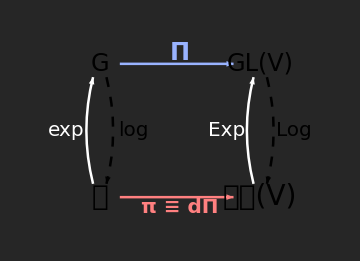

```mathematica
Graphics[{
(*Styles*)
Thickness[0.005],Arrowheads[0.04],
(*NODES*)
Text[Style["G",24,FontFamily->"Times"],{0,1}],
Text[Style["GL(V)",24,FontFamily->"Times"],{1.2,1}],
Text[Style["𝔤",28],{0,0}],
Text[Style["𝔤𝔩(V)",28],{1.2,0}],
(*HORIZONTAL ARROWS*)
(*Top Arrow: Π*)
{RGBColor[0.6,0.7,1.0],Arrow[{{0.15,1},{1.0,1}}],
Text[Style["Π",24,Bold],{0.6,1.08}]},
(*Bottom Arrow: π*)
{RGBColor[1.0,0.5,0.5],Arrow[{{0.15,0},{1.0,0}}],
Text[Style["π ≡ dΠ",20,Bold],{0.6,-0.08}]},
(*VERTICAL CURVED ARROWS (LEFT SIDE)*)
(*exp*)
{White,Arrow[BezierCurve[{{-0.05,0.1},{-0.15,0.5},{-0.05,0.9}}]],
Text[Style["exp",20,FontFamily->"Times"],{-0.25,0.5}]},
(*log*)
{Dashing[{0.02,0.02}],Arrow[BezierCurve[{{0.05,0.9},{0.15,0.5},{0.05,0.1}}]],
Text[Style["log",20,FontFamily->"Times"],{0.25,0.5}]},
(*VERTICAL CURVED ARROWS (RIGHT SIDE)*)
(*Exp*)
{White,Dashing[{}],Arrow[BezierCurve[{{1.15,0.1},{1.05,0.5},{1.15,0.9}}]],
Text[Style["Exp",20,FontFamily->"Times"],{0.95,0.5}]},
(*Log*)
{Dashing[{0.02,0.02}],Arrow[BezierCurve[{{1.25,0.9},{1.35,0.5},{1.25,0.1}}]],
Text[Style["Log",20,FontFamily->"Times"],{1.45,0.5}]}},
ImageSize->Medium,
PlotRange->{{-0.5,1.7},{-0.3,1.3}},
Background->GrayLevel[0.15]]
```

### Map the T-basis to the J-basis

#### T Basis → Matrix Rep

```mathematica
proof[2ⅈ T==Table[PauliMatrix[i],{i,3}]];
```

QED■

```mathematica
πMap[TMat_]:=
Module[{a,b,c},
{a,b,c}=ⅈ Tr[TMat.#]&/@(2 ⅈ T);
{a,b,c}.J]
(* generators-to-generators *)
(MatrixForm@*FullSimplify)/@(πMap[θ #]&/@T)
```

{(0 | 0 | 0
0 | 0 | -θ
0 | θ | 0),(0 | 0 | θ
0 | 0 | 0
-θ | 0 | 0),(0 | -θ | 0
θ | 0 | 0
0 | 0 | 0)}

#### Group Representation Map Π

```mathematica
With[{σ=PauliMatrix},
Πmap[U_]:=
Table[
1/2 Tr[σ[i].U.σ[j].U†], 
{i,3},{j,3}]];
(* rotations-to-rotations *)
(MatrixForm@*FullSimplify@*ComplexExpand)/@(Πmap[θ #]&/@T)
```

{(θ^2/4 | 0 | 0
0 | -θ^2/4 | 0
0 | 0 | -θ^2/4),(-θ^2/4 | 0 | 0
0 | θ^2/4 | 0
0 | 0 | -θ^2/4),(-θ^2/4 | 0 | 0
0 | -θ^2/4 | 0
0 | 0 | θ^2/4)}

```mathematica
proof@With[{id2=IdentityMatrix[2],
id3=IdentityMatrix[3]},
Πmap[-id2]==Πmap[id2]==id3];
```

QED■

```mathematica
ClearAll[commutativeDiagram];
commutativeDiagram[X_]:=
FullSimplify[
MatrixExp[πMap[X]]==
Πmap[MatrixExp[X]]//
ComplexExpand
];
proof[And@@commutativeDiagram/@(θ T)];
```

QED■

## The Big Beautiful Example

Here we show that a 3-vector rotated by an element of SU(2) maps to the same vector rotated by an element of SO(3). The reverse is twoS-to-one, as amply demonstrated above.

### ℝ^3 Vector ⟷ 𝔥_σ (Matrix-Vector)

```mathematica
ClearAll[toHσ,fromHσ];
toHσ[v_List]:=Total[v*T];
fromHσ[mat_]:=Table[-2 Tr[mat.T[[k]]],{k,3}];
```

### Rotation Parameters

```mathematica
Echo[vR3={x,y,z},"v_(ℝ^3) :"];
{ϕ,θ,ψ}={α,β,γ};
```

v_(ℝ^3) :  {x,y,z}

### SO(3) Rotation Matrix

#### R=R_z(ϕ).R_y(θ).R_x(ψ)=ⅇ^(ϕ J_3)ⅇ^(θ J_2)ⅇ^(ψ J_3)

```mathematica
Echo[(R=MatrixExp[ϕ J[[3]]].MatrixExp[θ J[[2]]].MatrixExp[ψ J[[1]]])//MatrixForm,"Rotation Matrix R_(ℝ^3) :"];
Echo[(vPrimeR3=Simplify[R.vR3])//MatrixForm,"v'_(ℝ^3) = R_(ℝ^3).v_(ℝ^3) :"];
```

Rotation Matrix R_(ℝ^3) :  (Cos[α] Cos[β] | -Cos[γ] Sin[α]+Cos[α] Sin[β] Sin[γ] | Cos[α] Cos[γ] Sin[β]+Sin[α] Sin[γ]
Cos[β] Sin[α] | Cos[α] Cos[γ]+Sin[α] Sin[β] Sin[γ] | Cos[γ] Sin[α] Sin[β]-Cos[α] Sin[γ]
-Sin[β] | Cos[β] Sin[γ] | Cos[β] Cos[γ])

v'_(ℝ^3) = R_(ℝ^3).v_(ℝ^3) :  (Sin[α] (-y Cos[γ]+z Sin[γ])+Cos[α] (x Cos[β]+Sin[β] (z Cos[γ]+y Sin[γ]))
Cos[α] (y Cos[γ]-z Sin[γ])+Sin[α] (x Cos[β]+Sin[β] (z Cos[γ]+y Sin[γ]))
-x Sin[β]+Cos[β] (z Cos[γ]+y Sin[γ]))

### SU(2) Unit Quaternion

#### Q_ϕθψ=ⅇ^(ϕ T_3)ⅇ^(θ T_3)ⅇ^(ψ T_3)

```mathematica
Echo[(Q=MatrixExp[ϕ T[[3]]].MatrixExp[θ T[[2]]].MatrixExp[ψ T[[1]]])//MatrixForm,"Q_ϕθψ :"];
```

Q_ϕθψ :  (ⅇ^(-(ⅈ α)/2) Cos[β/2] Cos[γ/2]+ⅈ ⅇ^(-(ⅈ α)/2) Sin[β/2] Sin[γ/2] | -ⅇ^(-(ⅈ α)/2) Cos[γ/2] Sin[β/2]-ⅈ ⅇ^(-(ⅈ α)/2) Cos[β/2] Sin[γ/2]
ⅇ^((ⅈ α)/2) Cos[γ/2] Sin[β/2]-ⅈ ⅇ^((ⅈ α)/2) Cos[β/2] Sin[γ/2] | ⅇ^((ⅈ α)/2) Cos[β/2] Cos[γ/2]-ⅈ ⅇ^((ⅈ α)/2) Sin[β/2] Sin[γ/2])

### Adjoint Action in 𝔥_σ

#### v_𝔥_0=to𝔥_σ(v_(ℝ^3))

```mathematica
Echo[(vHσ=toHσ[vR3])//MatrixForm,"v_𝔥_σ :"];
```

v_𝔥_σ :  (-(ⅈ z)/2 | -(ⅈ x)/2-y/2
-(ⅈ x)/2+y/2 | (ⅈ z)/2)

#### Q_ϕθψ v_𝔥_σ(Q†)_ϕθψ

```mathematica
Echo[(vPrimeHσ=Simplify[ComplexExpand[Q.vHσ.Q†]])//MatrixForm,"v'_𝔥_σ=Q :"];
```

v'_𝔥_σ=Q :  (-1/2 ⅈ (-x Sin[β]+Cos[β] (z Cos[γ]+y Sin[γ])) | -1/2 ⅈ (Cos[α]-ⅈ Sin[α]) (x Cos[β]+Cos[γ] (-ⅈ y+z Sin[β])+(ⅈ z+y Sin[β]) Sin[γ])
1/2 (-ⅈ Cos[α]+Sin[α]) (x Cos[β]+Cos[γ] (ⅈ y+z Sin[β])+(-ⅈ z+y Sin[β]) Sin[γ]) | 1/2 ⅈ (-x Sin[β]+Cos[β] (z Cos[γ]+y Sin[γ])))

### Proofs

#### Proof 1: Consistency of the Pauli Map

```mathematica
Echo[proof[Simplify[
fromHσ[toHσ[vR3]]==vR3
]],"Pauli Map Round Trip: ℝ^3 → 𝔥_σ → ℝ^3 :"];
```

QED■

Pauli Map Round Trip: ℝ^3 → 𝔥_σ → ℝ^3 :  True

#### Proof 2: SO(3) from SU(2)

Matrix elements of R_ϕθψ are R_ij=-2 Tr(T_j Q_ϕθψ T_j(Q†)_ϕθψ)

```mathematica
Echo[(RFromQ=Table[
-2Tr[T[[i]].Q.T[[j]].Q†]//
ComplexExpand//Simplify,
{i,3},{j,3}])//MatrixForm,"R_ij=-2Tr[T_i·Q·T_j·Q†] :"];
proof[RFromQ==R];
```

R_ij=-2Tr[T_i·Q·T_j·Q†] :  (Cos[α] Cos[β] | -Cos[γ] Sin[α]+Cos[α] Sin[β] Sin[γ] | Cos[α] Cos[γ] Sin[β]+Sin[α] Sin[γ]
Cos[β] Sin[α] | Cos[α] Cos[γ]+Sin[α] Sin[β] Sin[γ] | Cos[γ] Sin[α] Sin[β]-Cos[α] Sin[γ]
-Sin[β] | Cos[β] Sin[γ] | Cos[β] Cos[γ])

QED■

### Proof 3: Equivalence of the Rotated Vectors

Does the SU(2) rotated v'_𝔥_σ mat-vec map back to the SO(3) rotated vector v'_(ℝ^3)?

```mathematica
proof[Simplify[
fromHσ[vPrimeHσ]==vPrimeR3
]];
```

QED■

## References

Beckman, Brian (2026). SO(3) Gauge Theory for Classical Mechanics in 𝒰𝒟. Wolfram Community post.

Beckman, Brian. (2026) SU(2) Gauge Theory for Classical Mechanics in 𝒰𝒟. Wolfram Community post.

Hall, B. C. (2015). Lie Groups, Lie Algebras, and Representations: an Elementary Introduction, 2nd Edition, Springer. (Theorem 3.29)

Knapp, A. W. (2002). Lie Groups Beyond an Introduction. (Theorem 4.43).

Milnor, J. (1976). Curvatures of Left Invariant Metrics on Lie Groups. (Adv. Math. 21).

Georgi, H. (1999). Lie Algebras in Particle Physics: From Isospin to Unified Theories. Westview Press.

Humphreys, J. E. (1972). Introduction to Lie Algebras and Representation Theory. Springer.

Fuchs, J., & Schweigert, C. (1997). Symmetries, Lie Algebras and Representations: A Graduate Course for Physicists. Cambridge
     University Press.